# Target Probabilities with Quantum Circuits

## Introduction

This computational essay is part of work that focuses on quantum state preparation, an essential subroutine for quantum computing using the Wolfram quantum framework paclet . A high - level circuit model has been proposed [reference] that generates probability results in line with a random probability generator . Addressing the challenges in quantum computation’ logic model, a generic method is introduced for synthesizing quantum circuits capable of producing any desired quantum state from a given basis state, enabling both theoretical determination of upper bounds and experimental assessment of the required number of quantum gates [ref: Logic Synthesis for Quantum State Generation (2016 IEEE 46th International Symposium on Multiple-Valued Logic].  The work outlines a three step process for synthesizing the desired quantum circuit from a basis state, followed by a generalized method for generating n - qubit systems using a multiplexer function with controlled rotation gates and swap operations, aiming to provide a robust framework for the design and implementation of quantum circuits .

## Methodology

Quantum systems are composed of qubits. Qubits can be in one of the computational basis state |0> and |1>. More formally, a qubit can be described by a two-dimensional Hilbert space where its (quantum) state is given by unit vector so called state vector.
By inverting the resulting circuit , the desired quantum circuit transforming a basis state is synthesized. More precisely three steps are performed:

(a) Unify Phases: transformation of potentially different phases amplitudes to a single (global) phase.

(b) Unify probabilities: transformation of the potentially different moduli of amplitudes to an equal probability distribution.

(c) Remove superposition: transformation of unified amplitudes to a state with a single non-zero amplitude and, by this, generating a basis state (potentially with a negligible global phase).

Multiplexer function is used in our module to map various quantum circuits at one place (in this case controlled rotation gates)

Generalizing methods for generating n-qubit system is as follows:
(a) Multiplexer function followed by swapping {n,n-1}
(b) Multiplexer function followed by swapping {n,n-2}
(c) Multiplexer function followed by swapping {n,n-3}
.
.
.
.
(d) Multiplexer function followed by swapping {n,1}
(e) Finally apply Hadamard for realizing non-zero amplitude

## QPU setup

Wolfram quantum framework now comes with the IBM-Q service. We are utilizing it to access results from IBM  Quantum processors. We have mainly used two quantum processors namely: ibm_nairobi and ibmq_belem.

```mathematica
ibm=ServiceConnect["IBMQ","New"]
```

ServiceObject[…]

Extract ‘total qubits available’, ‘quantum_volume’ and ‘type of processor ‘ information of ibmq_belem and ibm_nairobi QPUs.

```mathematica
conf=ibm["Backend","ID"->"ibmq_belem","Property"->"Configuration"];
conf[{"n_qubits","processor_type","quantum_volume"}]
```

```mathematica
conf2=ibm["Backend","ID"->"ibm_nairobi","Property"->"Configuration"];
conf2[{"n_qubits","processor_type","quantum_volume"}]
```

You can find more information about handling of IBM quantum processors on Wolfram Quantum Framework here: https://community.wolfram.com/groups/-/m/t/2846060

#### About

In this computational essay, we aim to explore examples of different number of qubits namely Right state, Bell state and GHZ state on wolfram quantum framework. These states are measured in different basis(Pauli-Z, Pauli-X and Pauli-Y) state and their probabilities are extracted. The results show the robustness of the framework. Further, the circuits in different basis are encoded in qiskit model and sent to a real IBM quantum processor units(QPU) through query which is a recently introduced feature (‘ServiceConnect’) of the paclet. The result from the QPU is further analyzed and compared with the theoretical upper-bound. The result confirms the impact of noises as we scale the number of qubits in quantum circuit.

## Right State

A right state, also known as the + state, is a specific quantum state that is a balanced superposition of the basis states 0 and 1. Mathematically, the right state is represented as:	(0 + 1)/(√2)
The amplitudes of the basis states, 1/(√2) for both0 and 1, represent the probability amplitudes of finding the qubit in either the 0 or 1 state upon measurement.

### Define state

Define the right state.

```mathematica
ψ1=QuantumState["Right"];
```

Build the quantum circuit from above state and measure in different basis namely: Pauli-Z(Computational), Pauli-Y and Pauli-X

```mathematica
qcZ=QuantumCircuitOperator[ψ1]/*QuantumMeasurementOperator["Computational",{1}];
qcX=QuantumCircuitOperator[{"H"->{1},{1}}]@*QuantumCircuitOperator[ψ1];
qcY=QuantumCircuitOperator[{QuantumOperator["S"]["Dagger"]->1,"H"->1,{1}}]@*QuantumCircuitOperator[ψ1];
```

Decompose the above quantum circuit and convert in Qiskit format.

```mathematica
qiskitex1a=qcZ["Qiskit"]["Decompose"];
qiskitex1b=qcX["Qiskit"]["Decompose"];
qiskitex1c=qcY["Qiskit"]["Decompose"];
```

### QPU

Encode the converted circuit.(in this case PauliZ basis circuit)

```mathematica
qpyex1a=BaseEncode@qiskitex1a["QPY","Provider"->"IBMProvider","Backend"->"ibmq_belem"];
```

Send the query on backend and get its information.

```mathematica
idex1a=ibm["RunCircuit",{"QPY"->qpyex1a,"Backend"->"ibmq_belem"}];
```

Check the job status.

```mathematica
ibm["JobStatus",{"JobID"->Values[Normal[idex1a]][[1]]}]
```

Only when the job status gets completed, results can be obtained from below code.

Extract the QPU and WQF results.

```mathematica
dsex1a=ibm["JobResults",{"JobID"->Values[Normal[idex1a]][[1]]}];
dssex1a=Normal[dsex1a["results",All,"data","counts"]][[1]]
qpuResultsex1a=N@Normalize[Values@%,Total]
resultsex1a=qcZ[]["Probabilities"]
```

<|0x0→2099,0x1→1901|>

{0.52475,0.47525}

<|0→1/2,1→1/2|>

Similar approach is taken for Pauli-X and Pauli-Y circuits below.

```mathematica
qpyex1b=BaseEncode@qiskitex1b["QPY","Provider"->"IBMProvider","Backend"->"ibmq_belem"];
```

```mathematica
idex1b=ibm["RunCircuit",{"QPY"->qpyex1b,"Backend"->"ibmq_belem"}];
```

```mathematica
ibm["JobStatus",{"JobID"->Values[Normal[idex1b]][[1]]}]
```

```mathematica
dsex1b=ibm["JobResults",{"JobID"->Values[Normal[idex1b]][[1]]}];
dssex1b=Normal[dsex1b["results",All,"data","counts"]][[1]]
qpuResultsex1b=N@Normalize[Values@dssex1b,Total]
resultsex1b=qcX[]["Probabilities"]
```

<|0x0→2067,0x1→1933|>

{0.51675,0.48325}

<|0→1/2,1→1/2|>

```mathematica
qpyex1c=BaseEncode@qiskitex1c["QPY","Provider"->"IBMProvider","Backend"->"ibmq_belem"];
```

```mathematica
idex1c=ibm["RunCircuit",{"QPY"->qpyex1c,"Backend"->"ibmq_belem"}];
```

```mathematica
ibm["JobStatus",{"JobID"->Values[Normal[idex1c]][[1]]}]
```

```mathematica
dsex1c=ibm["JobResults",{"JobID"->Values[Normal[idex1c]][[1]]}];
dssex1c=Normal[dsex1c["results",All,"data","counts"]][[1]]
qpuResultsex1c=N@Normalize[Values@%,Total]
resultsex1c=qcY[]["Probabilities"]
```

<|0x0→3993,0x1→7|>

{0.99825,0.00175}

<|0→1,1→0|>

### Results

Plot the result (WQF and IBM QPU) in form of Bar chart and compare them side-by-side.

#### PauliZ

```mathematica
BarChart[Transpose[{Values[resultsex1a],qpuResultsex1a}],ChartLegends->{"Wolfram quantum framwork","IBM QPU"},PlotLabel->"Pauli-Z basis",LabelingFunction->(Callout[Row[{NumberForm[#,{2,2}]//N}],Automatic]&),ChartLabels->{{"0","1"},{"",""}}]
```

-Graphics-

#### PauliX

```mathematica
BarChart[Transpose[{Values[resultsex1b],qpuResultsex1b}],ChartLegends->{"Wolfram quantum framwork","IBM QPU"},PlotLabel->"Pauli-X basis",LabelingFunction->(Callout[Row[{NumberForm[#,{2,2}]//N}],Automatic]&),ChartLabels->{{"0","1"},{"",""}}]
```

-Graphics-

#### PauliY

```mathematica
BarChart[Transpose[{Values[resultsex1c],qpuResultsex1c}],ChartLegends->{"Wolfram quantum framwork","IBM QPU"},PlotLabel->"Pauli-Y basis",LabelingFunction->(Callout[Row[{NumberForm[#,{2,2}]//N}],Automatic]&),ChartLabels->{{"0","1"},{"",""}}]
```

-Graphics-

The result of WQF and IBM QPU matches to greater extent . The presence of noise in quantum processor (in this case ibm_nairobi) cause the mismatch in the result, however small here.

### Quantum State Estimate

Simulate measurement results in different basis state and find the corresponding quantum state estimation.

```mathematica
est1=QuantumStateEstimate[<|QuantumMeasurementOperator["X"]->Values@dssex1b,QuantumMeasurementOperator["Y"]->Values@dssex1c,QuantumMeasurementOperator["Z"]->Values@dssex1a|>]
```

QuantumStateEstimation[…]

Generate 100 states using the corresponding Bayesian sampling function.

```mathematica
sample1a=est1["BayesianSampler"][100];
```

Show histogram of fidelity with respect to the original quantum state.

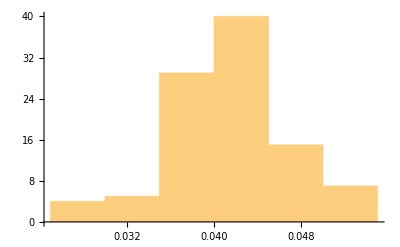

```mathematica
Histogram[QuantumDistance[#,ψ1,"Fidelity"]&/@sample1a]
```

### KS Test

KolmogorovSmirnovTest performs the Kolmogorov–Smirnov goodness-of-fit test with null hypothesis  that data(in this case measurement of right state in x, y and z basis) was drawn from a population with distribution(here simulated measurement in corresponding basis) and alternative hypothesis  that it was not.

List the qpu result of different basis.

```mathematica
qpu1z={2099,1901};
qpu1x={2067,1933};
qpu1y={3993,7};
```

Generate the simulated measurement on right state in X, Y and Z basis.

```mathematica
pz=Counts@QuantumMeasurementOperator[][QuantumState["Right"]]["SimulatedMeasurement",4000];
px=Counts@QuantumMeasurementOperator["X"][QuantumState["Right"]]["SimulatedMeasurement",4000];
py=Counts@QuantumMeasurementOperator["Y"][QuantumState["Right"]]["SimulatedMeasurement",4000];
```

Extract the X basis result

```mathematica
dataX=Values@Reverse@Join[AssociationThread[QuantumBasis["X"]["Names"],0],px]
```

{2005,1995}

Perform the KS test.

```mathematica
KolmogorovSmirnovTest[qpu1x,dataX]
```

1.

Extract the Y basis result and check the KS test.

```mathematica
dataY=Values@Reverse@Join[AssociationThread[QuantumBasis["Y"]["Names"],0],py]
```

{4000,0}

```mathematica
KolmogorovSmirnovTest[qpu1y,dataY]
```

1.

Extract the Z basis result.

```mathematica
dataZ=Values@Reverse@Join[AssociationThread[QuantumBasis[2]["Names"],0],pz]
```

{1974,2026}

Apply KS test.

```mathematica
KolmogorovSmirnovTest[qpu1z,dataZ]
```

1.

## ϕ_+ state

The ϕ_+ state, also known as the Bell state or EPR pair, is a specific example of a maximally entangled two-qubit state that  exhibits strong correlations between the qubits.
Mathematically, it is represented as: ϕ_+=1/(√2)(00+11)
The amplitudes of the basis states, 1/(√2) for both 00 and 11, represent the probability amplitudes of finding the two-qubit system in either state upon measurement. In this case, the probabilities of measuring the qubits in either the  00 or 11 state are equal, each being 1/2. The absence of other basis states, such as  01 and 10, indicates the entangled nature of the ϕ_+ state.

### Define state

Define the ϕ_+ state.

```mathematica
ψ2=QuantumState["Bell"];
```

Create quantum circuit in different basis (Pauli-Z, Pauli-X and Pauli-Y basis respectively)

```mathematica
qcZZ=QuantumMeasurementOperator[{1,2}]@QuantumCircuitOperator[ψ2];
qcXX=QuantumCircuitOperator[{"H"->{1,2},{1,2}}]@*QuantumCircuitOperator[ψ2];
qcYY=QuantumCircuitOperator[{QuantumOperator["S"]["Dagger"]->{1,2},"H"->{1,2},{1,2}}]@*QuantumCircuitOperator[ψ2];
```

Decompose the above quantum circuit and convert in Qiskit format.

```mathematica
qiskitex2a=qcZZ["Qiskit"]["Decompose"];
qiskitex2b=qcXX["Qiskit"]["Decompose"];
qiskitex2c=qcYY["Qiskit"]["Decompose"];
```

### QPU

Encode the converted circuit (in this case PauliZ basis circuit).

```mathematica
qpyex2a=BaseEncode@qiskitex2a["QPY","Provider"->"IBMProvider","Backend"->"ibmq_belem"];
```

Send the query on backend and get its information.

```mathematica
idex2a=ibm["RunCircuit",{"QPY"->qpyex2a,"Backend"->"ibmq_belem"}];
```

Check the job status.

```mathematica
ibm["JobStatus",{"JobID"->Values[Normal[idex2a]][[1]]}]
```

Extract the QPU and WQF results respectively.

```mathematica
dsex2a=ibm["JobResults",{"JobID"->Values[Normal[idex2a]][[1]]}];
dssex2a=Normal[dsex2a["results",All,"data","counts"]][[1]]
qpuResultsex2a=N@Normalize[Values@%,Total]
resultsex2a=qcZZ[]["Probabilities"]
```

<|0x0→1799,0x1→313,0x2→276,0x3→1612|>

{0.44975,0.07825,0.069,0.403}

<|00→1/2,01→0,10→0,11→1/2|>

Encode the above converted circuit, send the query on backend, get its information and extract the QPU results.(in this case PauliX basis circuit)

```mathematica
qpyex2b=BaseEncode@qiskitex2b["QPY","Provider"->"IBMProvider","Backend"->"ibmq_belem"];
```

```mathematica
idex2b=ibm["RunCircuit",{"QPY"->qpyex2b,"Backend"->"ibmq_belem"}];
```

```mathematica
ibm["JobStatus",{"JobID"->Values[Normal[idex2b]][[1]]}]
```

```mathematica
dsex2b=ibm["JobResults",{"JobID"->Values[Normal[idex2b]][[1]]}];
dssex2b=Normal[dsex2b["results",All,"data","counts"]][[1]]
qpuResultsex2b=N@Normalize[Values@%,Total]
resultsex2b=qcXX[]["Probabilities"]
```

<|0x0→1736,0x1→326,0x2→246,0x3→1692|>

{0.434,0.0815,0.0615,0.423}

<|00→1/2,01→0,10→0,11→1/2|>

Encode the above converted circuit again, send the query on backend, get its information and extract the QPU results . (in this case PauliY basis circuit)

```mathematica
qpyex2c=BaseEncode@qiskitex2c["QPY","Provider"->"IBMProvider","Backend"->"ibmq_belem"];
```

```mathematica
idex2c=ibm["RunCircuit",{"QPY"->qpyex2c,"Backend"->"ibmq_belem"}];
```

```mathematica
ibm["JobStatus",{"JobID"->Values[Normal[idex2c]][[1]]}]
```

```mathematica
dsex2c=ibm["JobResults",{"JobID"->Values[Normal[idex2c]][[1]]}];
dssex2c=Normal[dsex2c["results",All,"data","counts"]][[1]]
qpuResultsex2c=N@Normalize[Values@%,Total]
resultsex2c=qcYY[]["Probabilities"]
```

<|0x0→274,0x1→1948,0x2→1608,0x3→170|>

{0.0685,0.487,0.402,0.0425}

<|00→0,01→1/2,10→1/2,11→0|>

### Results

Plot the result (WQF and IBM QPU) in form of graphics(Bar Chart here) and compare them side-by-side.

#### PauliZ

```mathematica
BarChart[Transpose[{Values[resultsex2a],qpuResultsex2a}],ChartLegends->{"Wolfram quantum framwork","IBM QPU"},PlotLabel->"Pauli-Z basis",LabelingFunction->(Callout[Row[{NumberForm[#,{2,2}]//N}],Automatic]&),ChartLabels->{{"00","01","10","11"},{"","","",""}}]
```

-Graphics-

#### PauliX

```mathematica
BarChart[Transpose[{Values[resultsex2b],qpuResultsex2b}],ChartLegends->{"Wolfram quantum framwork","IBM QPU"},PlotLabel->"Pauli-X basis",LabelingFunction->(Callout[Row[{NumberForm[#,{2,2}]//N}],Automatic]&),ChartLabels->{{"00","01","10","11"},{"","","",""}}]
```

-Graphics-

#### PauliY

```mathematica
BarChart[Transpose[{Values[resultsex2c],qpuResultsex2c}],ChartLegends->{"Wolfram quantum framwork","IBM QPU"},PlotLabel->"Pauli-Y basis",LabelingFunction->(Callout[Row[{NumberForm[#,{2,2}]//N}],Automatic]&),ChartLabels->{{"00","01","10","11"},{"","","",""}}]
```

-Graphics-

The above comparison shows similar trend between WQF and IBM QPU.

### Quantum State Estimate

Simulate measurement results in different basis state and find the corresponding quantum state estimation.

```mathematica
est2=QuantumStateEstimate[<|QuantumMeasurementOperator["X",{1,2}]->Values@dssex2b,QuantumMeasurementOperator["Y",{1,2}]->Values@dssex2c,QuantumMeasurementOperator["Z",{1,2}]->Values@dssex2a|>]
```

QuantumStateEstimation[…]

Generate 100 states using the corresponding Bayesian sampling function.

```mathematica
sample2a=est2["BayesianSampler"][100];
```

Show histogram of fidelity with respect to the original quantum state.

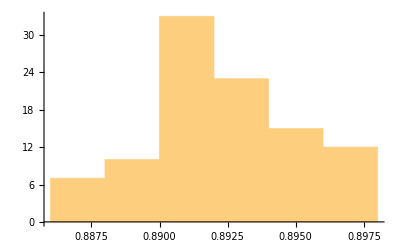

```mathematica
Histogram[QuantumDistance[#,ψ2,"Fidelity"]&/@sample2a]
```

### KS Test

Perform the KS test on the 2-qubit bell state in different basis and test the fit of qpu data(generated above) to a SimulatedMeasurement distribution.

List all qpu results.

```mathematica
qpu2z={1799, 313, 276, 1612};
qpu2x={1736, 326, 246, 1692};
qpu2y={274, 1948, 1608, 170};
```

```mathematica
pzz=Counts@QuantumMeasurementOperator[{1,2}][QuantumState["PhiPlus"]]["SimulatedMeasurement",4000];
pxx=Counts@QuantumMeasurementOperator["X",{1,2}][QuantumState["PhiPlus"]]["SimulatedMeasurement",4000];
pyy=Counts@QuantumMeasurementOperator["Y",{1,2}][QuantumState["PhiPlus"]]["SimulatedMeasurement",4000];
```

```mathematica
pxx
```

<|ψ_(x_+)ψ_(x_+)→1938,ψ_(x_-)ψ_(x_-)→2062|>

```mathematica
dataXX=Values@Reverse@Join[AssociationThread[QuantumBasis["X",2]["Names"],0],pxx]
```

{1938,0,0,2062}

```mathematica
KolmogorovSmirnovTest[qpu2x,dataXX]
```

0.771429

```mathematica
pyy
```

<|ψ_(y_-)ψ_(y_+)→2015,ψ_(y_+)ψ_(y_-)→1985|>

```mathematica
dataYY=Values@Reverse@Join[AssociationThread[QuantumBasis["Y",2]["Names"],0],pyy]
```

{0,1985,2015,0}

```mathematica
KolmogorovSmirnovTest[qpu2y,dataYY]
```

0.771429

```mathematica
pzz
```

<|00→2003,11→1997|>

```mathematica
dataZZ=Values@Reverse@Join[AssociationThread[QuantumBasis[2,2]["Names"],0],pzz]
```

{1997,0,0,2003}

```mathematica
KolmogorovSmirnovTest[qpu2z,dataZZ]
```

0.771429

## GHZ state

The Greenberger-Horne-Zeilinger (GHZ) state is a specific example of a multipartite entangled state involving three or more qubits. GHZ states are particularly interesting because they exhibit strong correlations among all the qubits involved, making them a valuable tool for studying entanglement properties and quantum nonlocality.
For a three-qubit system, the GHZ state is represented as: 1/(√2)(∣000⟩+∣111⟩)
The amplitudes of the basis states, 1/(√2) for both 000and 111, represent the probability amplitudes of finding the three-qubit system in either the  000or 111 state upon measurement. In this case, the probabilities of measuring the qubits in either of the state are equal, each being 1/2.

### Define state

Define GHZ state

```mathematica
ψ3=QuantumState["GHZ"];
```

Create quantum circuit using the above state in different basis.

```mathematica
qcZZZ=QuantumMeasurementOperator[{1,2,3}]@QuantumCircuitOperator[ψ3];
qcXXX=QuantumCircuitOperator[{"H"->{1,2,3},{1,2,3}}]@*QuantumCircuitOperator[ψ3];
qcYYY=QuantumCircuitOperator[{QuantumOperator["S"]["Dagger"]->{1,2,3},"H"->{1,2,3},{1,2,3}}]@*QuantumCircuitOperator[ψ3];
```

Extract the parameters.

```mathematica
{names3ea,params3ea}=Reap[QuantumLabelName[qcZZZ],_,Rule];
{names3eb,params3eb}=Reap[QuantumLabelName[qcXXX],_,Rule];
{names3ec,params3ec}=Reap[QuantumLabelName[qcYYY],_,Rule];
```

Note that qiskit conversion fallbacks to unitaries, which is not good for transpiling on QPU, therefore different treatment compared to example cases.

```mathematica
qiskitex3a=QuantumCircuitOperator[names3ea]["Qiskit"]["Decompose"];
qiskitex3b=QuantumCircuitOperator[names3eb]["Qiskit"]["Decompose"];
qiskitex3c=QuantumCircuitOperator[names3ec]["Qiskit"]["Decompose"];
```

### QPU

We use the similar approach to run above GHZ quantum circuit: 
(i) Encode the converted circuit (PauliZ, PauliX, PauliY basis circuit)
(ii) Send the query on backend and get its information.
(iii) Check the job status. Run below steps only when the status is completed.
(iv) Extract the QPU and WQF results respectively.
(v) Plot the results on bar graph and compare.

```mathematica
qpyex3a=BaseEncode@qiskitex3a["QPY","Provider"->"IBMProvider","Backend"->"ibmq_belem"];
```

```mathematica
idex3a=ibm["RunCircuit",{"QPY"->qpyex3a,"Backend"->"ibmq_belem"}];
```

```mathematica
ibm["JobStatus",{"JobID"->Values[Normal[idex3a]][[1]]}]
```

```mathematica
dsex3a=ibm["JobResults",{"JobID"->Values[Normal[idex3a]][[1]]}];
dssex3a=Normal[dsex3a["results",All,"data","counts"]][[1]]
qpuResultsex3a=N@Normalize[Values@%,Total]
resultsex3a=qcZZZ[]["Probabilities"]
```

<|0x0→605,0x1→574,0x2→629,0x3→614,0x4→406,0x5→340,0x6→386,0x7→446|>

{0.15125,0.1435,0.15725,0.1535,0.1015,0.085,0.0965,0.1115}

<|000→1/2,001→0,010→0,011→0,100→0,101→0,110→0,111→1/2|>

```mathematica
qpyex3b=BaseEncode@qiskitex3b["QPY","Provider"->"IBMProvider","Backend"->"ibmq_belem"];
```

```mathematica
idex3b=ibm["RunCircuit",{"QPY"->qpyex3b,"Backend"->"ibmq_belem"}];
```

```mathematica
ibm["JobStatus",{"JobID"->Values[Normal[idex3b]][[1]]}]
```

```mathematica
dsex3b=ibm["JobResults",{"JobID"->Values[Normal[idex3b]][[1]]}];
dssex3b=Normal[dsex3b["results",All,"data","counts"]][[1]]
qpuResultsex3b=N@Normalize[Values@%,Total]
resultsex3b=qcXXX[]["Probabilities"]
```

<|0x0→553,0x1→411,0x2→527,0x3→394,0x4→644,0x5→441,0x6→628,0x7→402|>

{0.13825,0.10275,0.13175,0.0985,0.161,0.11025,0.157,0.1005}

<|000→1/4,001→0,010→0,011→1/4,100→0,101→1/4,110→1/4,111→0|>

```mathematica
qpyex3c=BaseEncode@qiskitex3c["QPY","Provider"->"IBMProvider","Backend"->"ibmq_belem"];
```

```mathematica
idex3c=ibm["RunCircuit",{"QPY"->qpyex3c,"Backend"->"ibmq_belem"}];
```

```mathematica
ibm["JobStatus",{"JobID"->Values[Normal[idex3c]][[1]]}]
```

```mathematica
dsex3c=ibm["JobResults",{"JobID"->Values[Normal[idex3c]][[1]]}];
dssex3c=Normal[dsex3c["results",All,"data","counts"]][[1]]
qpuResultsex3c=N@Normalize[Values@%,Total]
resultsex3c=qcYYY[]["Probabilities"]
```

<|0x0→514,0x1→559,0x2→561,0x3→598,0x4→435,0x5→426,0x6→445,0x7→462|>

{0.1285,0.13975,0.14025,0.1495,0.10875,0.1065,0.11125,0.1155}

<|000→1/8,001→1/8,010→1/8,011→1/8,100→1/8,101→1/8,110→1/8,111→1/8|>

### Results

Plot the result (WQF and IBM QPU) on Bar Chart and compare them side - by - side .

#### PauliZ

```mathematica
BarChart[Transpose[{Values[resultsex3a],qpuResultsex3a}],ChartLegends->{"Wolfram quantum framwork","IBM QPU"},PlotLabel->"Pauli-Z basis",LabelingFunction->(Callout[Row[{NumberForm[#,{2,2}]//N}],Automatic]&),ChartStyle->"Rainbow",ChartLabels->{{"000","001","010","011","100","101","110","111"},{"","","","","","","",""}}]
```

-Graphics-

#### PauliX

```mathematica
BarChart[Transpose[{Values[resultsex3b],qpuResultsex3b}],ChartLegends->{"Wolfram quantum framwork","IBM QPU"},PlotLabel->"Pauli-X basis",LabelingFunction->(Callout[Row[{NumberForm[#,{2,2}]//N}],Automatic]&),ChartStyle->"Rainbow",ChartLabels->{{"000","001","010","011","100","101","110","111"},{"","","","","","","",""}}]
```

-Graphics-

#### PauliY

```mathematica
BarChart[Transpose[{Values[resultsex3c],qpuResultsex3c}],ChartLegends->{"Wolfram quantum framwork","IBM QPU"},PlotLabel->"Pauli-Y basis",LabelingFunction->(Callout[Row[{NumberForm[#,{2,2}]//N}],Automatic]&),ChartStyle->"Rainbow",ChartLabels->{{"000","001","010","011","100","101","110","111"},{"","","","","","","",""}}]
```

-Graphics-

The above comparison shows very different trend between WQF and IBM QPU result mainly for Pauli-Z and Paulli-X basis measurement circuit. It most certainly affirms impact of noise in quantum circuit which utilises higher number of qubits. This can be reduced by doing optimization or similar methods. The impact of noised can further be studied by fidelity and decoherence in the circuit.

### Quantum State Estimate

Simulate measurement results in different basis state and find the corresponding quantum state estimation.

```mathematica
est3=QuantumStateEstimate[<|QuantumMeasurementOperator["X",{1,2,3}]->Values@dssex3b,QuantumMeasurementOperator["Y",{1,2,3}]->Values@dssex3c,QuantumMeasurementOperator["Z",{1,2,3}]->Values@dssex3a|>]
```

QuantumStateEstimation[…]

Generate 100 states using the corresponding Bayesian sampling function.

```mathematica
sample3a=est3["BayesianSampler"][100];
```

Show histogram of fidelity with respect to the original quantum state.

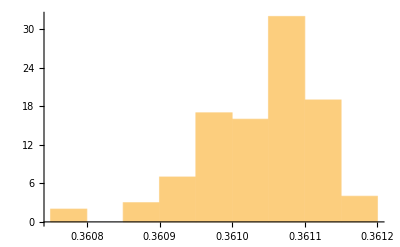

```mathematica
Histogram[QuantumDistance[#,ψ3,"Fidelity"]&/@sample3a]
```

### KS Test

Perform the KS test on the GHZ state in different basis and test the fit of qpu data to a SimulatedMeasurement distribution.

List all qpu counts generated above.

```mathematica
qpu3z = {605, 574, 629, 614, 406, 340, 386, 446};
qpu3x = {553, 411, 527, 394, 644, 441, 628, 402};
qpu3y = {514, 559, 561, 598, 435, 426, 445, 462};
```

```mathematica
pzzz = Counts@
   QuantumMeasurementOperator[{1, 2, 3}][QuantumState["GHZ"]][
    "SimulatedMeasurement", 4000];
pxxx = Counts@
   QuantumMeasurementOperator["X", {1, 2, 3}][QuantumState["GHZ"]][
    "SimulatedMeasurement", 4000];
pyyy = Counts@
   QuantumMeasurementOperator["Y", {1, 2, 3}][QuantumState["GHZ"]][
    "SimulatedMeasurement", 4000];
```

```mathematica
pxxx
```

<|ψ_(x_-)ψ_(x_+)ψ_(x_-)→1039,ψ_(x_+)ψ_(x_-)ψ_(x_-)→1027,ψ_(x_-)ψ_(x_-)ψ_(x_+)→956,ψ_(x_+)ψ_(x_+)ψ_(x_+)→978|>

```mathematica
dataXXX = 
 Values@Reverse@
   Join[AssociationThread[QuantumBasis["X", 3]["Names"], 0], pxxx]
```

{978,0,0,1027,0,1039,956,0}

```mathematica
KolmogorovSmirnovTest[qpu3x, dataXXX]
```

0.282673

```mathematica
pyyy
```

<|ψ_(y_+)ψ_(y_-)ψ_(y_-)→497,ψ_(y_-)ψ_(y_-)ψ_(y_-)→489,ψ_(y_-)ψ_(y_+)ψ_(y_-)→527,ψ_(y_+)ψ_(y_-)ψ_(y_+)→510,ψ_(y_-)ψ_(y_-)ψ_(y_+)→495,ψ_(y_+)ψ_(y_+)ψ_(y_+)→556,ψ_(y_-)ψ_(y_+)ψ_(y_+)→429,ψ_(y_+)ψ_(y_+)ψ_(y_-)→497|>

```mathematica
dataYYY = 
 Reverse[Values[pyyy]]
```

{497,429,556,495,510,527,489,497}

```mathematica
KolmogorovSmirnovTest[qpu3y, dataYYY]
```

0.66014

```mathematica
pzzz
```

<|000→2035,111→1965|>

```mathematica
dataZZZ= Join[Reverse[Values[pzzz]],{0,0,0,0,0,0}]
```

{1965,2035,0,0,0,0,0,0}

```mathematica
KolmogorovSmirnovTest[qpu3z, dataZZZ]
```

0.018648

## References

Logic Synthesis for Quantum State Generation paper by Philipp Niemann, Rhitam Datta,Robert Wille (2016 IEEE 46th International Symposium on Multiple-Valued Logic)

Quantum state preparation with optimal circuits depth: Implementations and Applications by Xiao-Ming Zhang, Tongyang Li and Xiao Yuan (arXiv:2201.11495v3 [quant-ph] 5 Dec 2022

Circuits for measurement based quantum state preparation paper by Niels Gleinig and Torsten Hoefler

https://wolfr.am/wolfram-quantum

https://community.wolfram.com/groups/-/m/t/2777794

https://community.wolfram.com/groups/-/m/t/2846060

## Initialization cells

```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]